```mathematica
<<Datasets`
<<Plots`
```

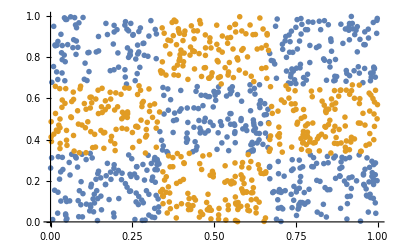

```mathematica
ds=DatasetImport["D:\\Projects.github\\python_projects\\article_distillation\\data_reg\\Xy-1kx2.csv", "HeaderLines"->1];
l0 = ds[Select[#y==0&]][[All, {"x0","x1"}]];
l1 = ds[Select[#y==1&]][[All, {"x0","x1"}]];
ListPointPlot[{l0,l1},PlotStyle->{PointSize->.01}]
```

```mathematica
ds=DatasetImport["D:\\Projects.github\\python_projects\\article_distillation\\data_reg\\Xy-10kx3.csv", "HeaderLines"->1];
l0 = ds[Select[#y==0&]][[All, {"x0","x1", "x2"}]];
l1 = ds[Select[#y==1&]][[All, {"x0","x1", "x2"}]];
ListPointPlot3D[{l0,l1},PlotStyle->{PointSize->.01}]
```

-Graphics3D-